# Preserved A–φ field diagnostics

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

J=−σ(jωA+∇φ); ∇·J=0

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Read actual saved fields and reproduce J, phi and gauge residuals. Original field parameters remain visible.

## Derivation and interpretation

Under exp(+jωt), reconstruct J=−σ(jωA+∇φ) from the original saved A and φ fields. Compare current conservation and normalized potential/gauge residuals using the exact preserved inputs.

This entry changes only diagnostic sampling density. It recomputes derivatives on saved fields and tests reproducibility against the original diagnostic quantities; it performs no new field solve.

The saved scalar-potential/gauge checks remain failed. Preserve mesh, excitation, gauge and boundary assumptions. Continue only after identifying a consistent formulation and passing conservation, gauge and mesh studies.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"sampling_points"->32|>;parameters
```

<|sampling_points -> 32|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"aphi",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_aphi_20261014075257_a89f63c5, source_model -> aphi, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> failed_retained_phi_gauge|>

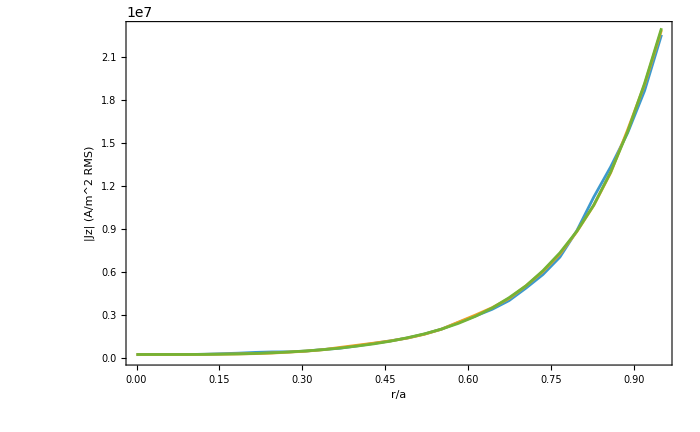

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: FEMDOC, GMRES1986; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch aphi